```mathematica
Integrate[(ψ0+(ψh-ψ0)/h x)^2,{x,0,h}]
```

1/3 h (ψ0^2+ψ0 ψh+ψh^2)

```mathematica
Simplify[Integrate[(ψ0+(ψh-ψ0)/h x)(ϕ0+(ϕh-ϕ0)/h x),{x,0,h}]]
```

1/6 h (ϕ0 (2 ψ0+ψh)+ϕh (ψ0+2 ψh))

```mathematica
(* make the H matrix *)
makeH[N_]:=Module[{h=1/(N+1),res=ConstantArray[0,{N,N}]},
Do[res[[i,i]]+=2h^-2,{i,1,N}];
Do[res[[i,i+1]]-=h^-2;res[[i+1,i]]-=h^-2,{i,1,N-1}];
res]
```

```mathematica
(* integrate the square of a function in an interval *)
intsq[ψ0_,ψh_,h_]:=1/3 h (ψ0^2+ψ0 ψh+ψh^2);
```

```mathematica
(* normalize an eigenvector of the Hamiltonian *)
normal[ψ_,N_]:=Module[{},res=0;
res+=intsq[0,ψ[[1]],1/(N+1)];
Do[res+=intsq[ψ[[i]],ψ[[i+1]],1/(N+1)],{i,1,N-1}];
res+=intsq[ψ[[N]],0,1/(N+1)];
1/Sqrt[res]]
```

```mathematica
(* use values to get the value at a specified location *)
interp[ψ0_,ψh_,h_,x_]:=Module[{},ψ0+(ψh-ψ0)/h x];
```

```mathematica
(* render a piecewise cubic function from a renormalized eigenvector *)
render[ψ_,N_,x_]:=Module[{i=IntegerPart[x*(N+1)]},
If[i==N+1,i-=1,];
If[i==0,res=interp[0,ψ[[1]],1/(N+1),x-i/(N+1)],];
If[0<i<N,res=interp[ψ[[i]],ψ[[i+1]],1/(N+1),x-i/(N+1)],];
If[i==N,res=interp[ψ[[N]],0,1/(N+1),x-i/(N+1)],];
res]
```

```mathematica
(* N = 2 case *)
HH2=makeH[2];
MatrixPlot[HH2];
```

```mathematica
{EE2,ψψ2}=Eigensystem[HH2]
```

{{27,9},{{-1,1},{1,1}}}

```mathematica
N[EE2/(Range[2,1,-1]Pi)^2,16]
```

{0.68391798958578,0.9118906527810399}

```mathematica
NN2=Table[normal[ψψ2[[i]],2],{i,2}]
```

{√3,3/(√5)}

```mathematica
MatrixPlot[Sign[ψψ2[[All,1]]]*NN2*ψψ2];
```

```mathematica
plotψ2[i_]:=Plot[{√2 Sin[(3-i)Pi x],render[Sign[ψψ2[[i,1]]]*NN2[[i]]*ψψ2[[i]],2,x]},{x,0,1}];
```

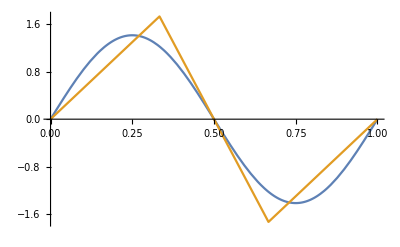

```mathematica
plotψ2[1]
```

```mathematica
(* N = 4 case *)
HH4=makeH[4];
MatrixPlot[HH4];
```

```mathematica
{EE4,ψψ4}=Eigensystem[HH4]
```

{{25/2 (5+√5),25/2 (3+√5),-25/2 (-5+√5),-25/2 (-3+√5)},{{-1,1/2 (1+√5),1/2 (-1-√5),1},{1,1/2 (1-√5),1/2 (1-√5),1},{-1,1/2 (1-√5),1/2 (-1+√5),1},{1,1/2 (1+√5),1/2 (1+√5),1}}}

```mathematica
N[EE4/(Range[4,1,-1]Pi)^2,16]
```

{0.5727866971849186,0.7368397293222504,0.8751402000833808,0.967531209275079}

```mathematica
NN4=Table[normal[ψψ4[[i]],4],{i,4}];
```

```mathematica
MatrixPlot[Sign[ψψ4[[All,4]]]*NN4*ψψ4];
```

```mathematica
plotψ4[i_]:=Plot[{√2 Sin[(5-i)Pi x],render[Sign[ψψ4[[i,1]]]*NN4[[i]]*ψψ4[[i]],4,x]},{x,0,1}];
```

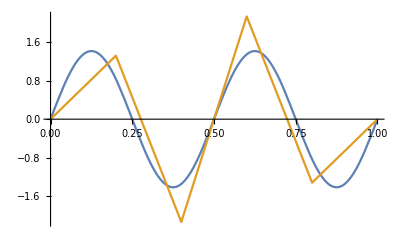

```mathematica
plotψ4[1]
```

```mathematica
(* N = 8 case *)
HH8=makeH[8];
MatrixPlot[HH8];
```

```mathematica
{EE8,ψψ8}=N[Eigensystem[HH8],16];
```

```mathematica
N[EE8/(Range[8,1,-1]Pi)^2,16]
```

{0.4974715041083517,0.5915899910483607,0.68391798958578,0.770571938064942,0.8477353155308679,0.9118906527810399,0.9600384846869408,0.989887237182931}

```mathematica
NN8=Table[normal[ψψ8[[i]],8],{i,8}];
```

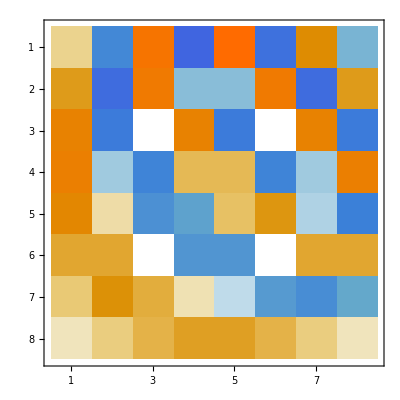

```mathematica
MatrixPlot[Sign[ψψ8[[All,1]]]*NN8*ψψ8]
```

```mathematica
plotψ8[i_]:=Plot[{√2 Sin[(9-i)Pi x],render[Sign[ψψ8[[i,1]]]*NN8[[i]]*ψψ8[[i]],8,x]},{x,0,1}];
```

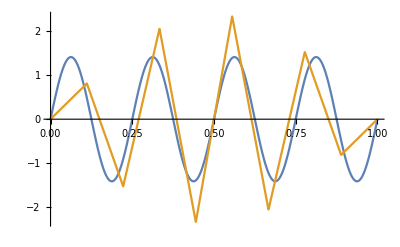

```mathematica
plotψ8[1]
```

```mathematica
(* N = 16 case *)
HH16=makeH[16];
MatrixPlot[HH16];
```

```mathematica
{EE16,ψψ16}=N[Eigensystem[HH16],16];
```

```mathematica
N[EE16/(Range[16,1,-1]Pi)^2,16]
```

{0.4536333240606777,0.5029894042820251,0.5528339690222047,0.6026195230388409,0.6517786426375064,0.6997331123542704,0.7459034611158359,0.7897187100586175,0.8306261371217882,0.8681008607950791,0.9016550471021039,0.9308465500296614,0.9552868060611466,0.9746478180211486,0.9886680817717043,0.9971573310089825}

```mathematica
NN16=Table[normal[ψψ16[[i]],16],{i,16}];
```

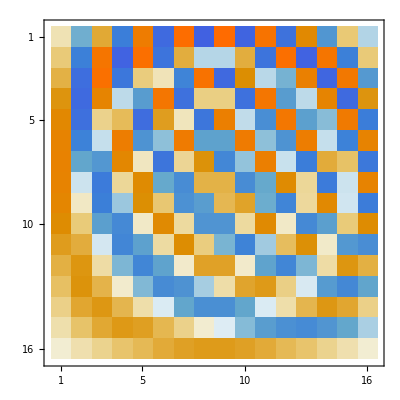

```mathematica
MatrixPlot[Sign[ψψ16[[All,1]]]*NN16*ψψ16]
```

```mathematica
plotψ16[i_]:=Plot[{√2 Sin[(17-i)Pi x],render[Sign[ψψ16[[i,1]]]*NN16[[i]]*ψψ16[[i]],16,x]},{x,0,1}];
```

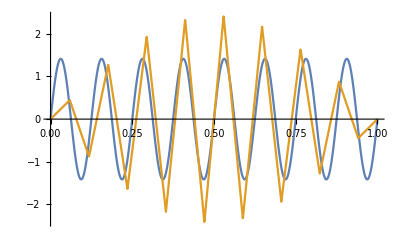

```mathematica
plotψ16[1]
```

```mathematica
(* N = 32 case *)
HH32=makeH[32];
MatrixPlot[HH32];
```

```mathematica
{EE32,ψψ32}=N[Eigensystem[HH32],16];
```

```mathematica
N[EE32/(Range[32,1,-1]Pi)^2,16]
```

{0.430034991179395,0.4551166965140401,0.4804623167696253,0.506001769041727,0.5316626995475987,0.5573707769674827,0.5830499994628942,0.608623013838887,0.6340114452348205,0.6591362356548536,0.68391798958578,0.7082773248963596,0.7321352271693689,0.7554134055855127,0.778034648457369,0.7999231765018484,0.8210049919413638,0.8412082215370479,0.8604634516819042,0.8787040537176081,0.8958664976856162,0.9118906527810399,0.9267200728460579,0.9403022653181078,0.952588942136234,0.9635362512062622,0.9731049871313463,0.9812607800282373,0.9879742613706845,0.9932212059289486,0.9969826490077079,0.9992449783228591}

```mathematica
NN32=Table[normal[ψψ32[[i]],32],{i,32}];
```

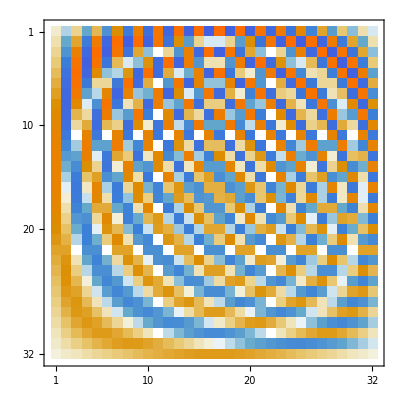

```mathematica
MatrixPlot[Sign[ψψ32[[All,1]]]*NN32*ψψ32]
```

```mathematica
plotψ32[i_]:=Plot[{√2 Sin[(33-i)Pi x],render[Sign[ψψ32[[i,1]]]*NN32[[i]]*ψψ32[[i]],32,x]},{x,0,1}];
```

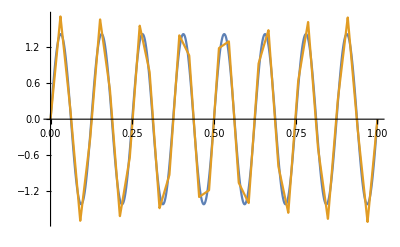

```mathematica
plotψ32[17]
```

```mathematica
(* N = 64 case *)
HH64=N[makeH[64],16];
MatrixPlot[HH64];
```

```mathematica
{EE64,ψψ64}=N[Eigensystem[HH64],16];
```

```mathematica
N[EE64/(Range[64,1,-1]Pi)^2,16]
```

{0.4178047358904063,0.430418522865611,0.443117523547467,0.4558929793599607,0.4687359537996135,0.4816373414291008,0.4945878771524177,0.5075781457600957,0.5205985917325256,0.5336395292890023,0.5466911526696896,0.5597435466373016,0.5727866971849186,0.5858105024359893,0.5988047837222339,0.6117592968248409,0.6246637433640505,0.6375077823219447,0.6502810416830052,0.6629731301767738,0.6755736491067417,0.6880722042494082,0.7004584178072951,0.7127219403995636,0.724852463073775,0.7368397293222504,0.7486735470864254,0.760343800732562,0.771840462982174,0.7831536067805365,0.794273417086696,0.8051902025684659,0.8158944071859854,0.8263766216475419,0.8366275947215013,0.8466382443883601,0.8563996688171313,0.8659031571504939,0.8751402000833808,0.8841025002199494,0.89278198219417,0.9011708025395836,0.9092613592941168,0.9170463013262052,0.9245185373688536,0.9316712447486688,0.9384978777973224,0.9449921759333426,0.9511481714025994,0.9569601966663265,0.9624228914260209,0.967531209275079,0.9722804239675564,0.9766661352949878,0.9806842745627623,0.9843311096581247,0.9876032497024619,0.9904976492811285,0.9930116122446798,0.9951427950759959,0.9968892098184103,0.9982492265605918,0.9992215754745713,0.9998053484039525}

```mathematica
NN64=Table[normal[ψψ64[[i]],64],{i,64}];
```

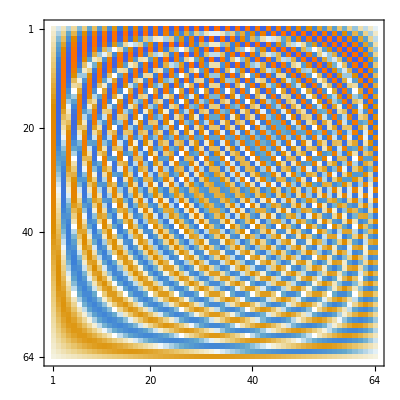

```mathematica
MatrixPlot[Sign[ψψ64[[All,1]]]*NN64*ψψ64]
```

```mathematica
plotψ64[i_]:=Plot[{√2 Sin[(65-i)Pi x],render[Sign[ψψ64[[i,1]]]*NN64[[i]]*ψψ64[[i]],64,x]},{x,0,1}];
```

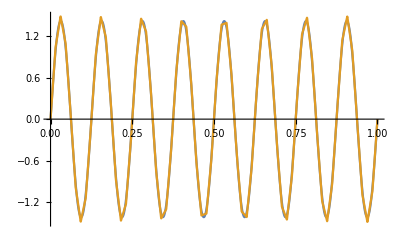

```mathematica
plotψ64[49]
```

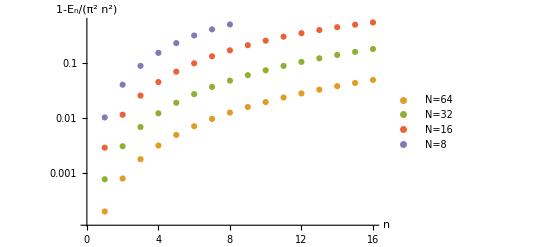

```mathematica
ListLogPlot[{1-Reverse[EE64[[Range[-16,-1]]]]/(Range[16]Pi)^2,1-Reverse[EE32[[Range[-16,-1]]]]/(Range[16]Pi)^2,
1-Reverse[EE16]/(Range[16]Pi)^2,
1-Reverse[EE8]/(Range[8]Pi)^2},
AxesLabel->{n,1-Subscript["E",n]/(n π)^2},
PlotLegends->Placed[{"N=64","N=32","N=16","N=8"},{Right,Bottom}],PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351]}]
```

```mathematica
(* need to comment out some lines as n increases *)
plotψs[n_]:=Module[{},
Plot[{√2 Sin[n Pi x],render[Sign[ψψ64[[-n,1]]]*NN64[[-n]]*ψψ64[[-n]],64,x],render[Sign[ψψ32[[-n,1]]]*NN32[[-n]]*ψψ32[[-n]],32,x],render[Sign[ψψ16[[-n,1]]]*NN16[[-n]]*ψψ16[[-n]],16,x](*,render[Sign[ψψ8[[-n,1]]]*NN8[[-n]]*ψψ8[[-n]],8,x]*)},{x,0,1}(*,PlotLegends->Placed[{"Exact","N=64","N=32","N=16","N=8"},{Center,Center}]*)]]
```

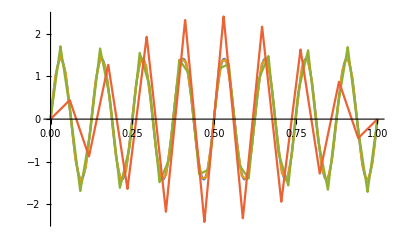

```mathematica
plotψs[16]
```